# SU(2) in 1+2D

```mathematica
coord={t,x,y};
n=3;(*# of spacetime dimensions*)
```

```mathematica
(*Minkowski*)
```

```mathematica
gdd={{-1,0,0},{0,1,0},{0,0,1}};
gUU= {{-1,0,0},{0,1,0},{0,0,1}};
```

```mathematica
(*Christoffel  symbols*)
```

```mathematica
ΓUdd=Table[1/2 Sum[gUU[[i]][[l]](D[gdd[[l]][[k]],coord[[j]]]+D[gdd[[l]][[j]],coord[[k]]]-D[ gdd[[j]][[k]],coord[[l]]]),{l,1,n}],{i,1,n},{j,1,n},{k,1,n}];
```

```mathematica
(*Gauge field A with 'a' as internal index and d as spacetime index= Aad*)
```

```mathematica
m=3;(*# of internal indices (SU(2))*)
```

```mathematica
Aad={{0,Subscript[A, 1,1][t],Subscript[A, 1,2][t]},{0,Subscript[A, 2,1][t],Subscript[A, 2,2][t]},{0,Subscript[A, 3,1][t],Subscript[A, 3,2][t]}}
```

{{0,A_(1,1)[t],A_(1,2)[t]},{0,A_(2,1)[t],A_(2,2)[t]},{0,A_(3,1)[t],A_(3,2)[t]}}

```mathematica
MatrixForm[Aad]
```

(0 | A_(1,1)[t] | A_(1,2)[t]
0 | A_(2,1)[t] | A_(2,2)[t]
0 | A_(3,1)[t] | A_(3,2)[t])

```mathematica
(*Field strength tensor(Subscript[F, μν])*)
```

```mathematica
Fadd=Table[D[Aad[[a]][[j]],coord[[i]]]- D[Aad[[a]][[i]],coord[[j]]] +g Sum[LeviCivitaTensor[3] [[a,b,c]] Aad[[b]][[i]]Aad[[c]][[j]],{b,1,m},{c,1,m}],{a,1,m},{i,1,n},{j,1,n}];
```

```mathematica
Fadd[[3]]//MatrixForm
```

(0 | A_(3,1)'[t] | A_(3,2)'[t]
-A_(3,1)'[t] | 0 | g (-A_(1,2)[t] A_(2,1)[t]+A_(1,1)[t] A_(2,2)[t])
-A_(3,2)'[t] | g (A_(1,2)[t] A_(2,1)[t]-A_(1,1)[t] A_(2,2)[t]) | 0)

```mathematica
(*F^aμν*)
```

```mathematica
FaUU=Table[Sum[gUU[[i]][[k]]gUU[[j]][[l]]Fadd[[a]][[k]][[l]],{k,1,n},{l,1,n}],{a,1,m},{i,1,n},{j,1,n}];
```

```mathematica
(*EM tensor*)
```

```mathematica
Tμν=Table[Sum[gUU[[α]][[β]] Fadd[[a]][[μ]][[α]]Fadd[[a]][[ν]][[β]],{a,1,m},{α,1,n},{β,1,n}],{μ,1,n},{ν,1,n}]-1/4 Table[gdd[[μ]][[ν]],{μ,1,n},{ν,1,n}]Sum[FaUU[[a]][[α]][[β]]Fadd[[a]][[α]][[β]],{a,1,m},{α,1,n},{β,1,n}];
```

```mathematica
Tμν//MatrixForm
```

(3 u'[t]^2+1/4 (6 q^2 u[t]^4-6 u'[t]^2) | 0 | 0 | 0
0 | 2 q^2 u[t]^4-u'[t]^2+1/4 (-6 q^2 u[t]^4+6 u'[t]^2) | 0 | 0
0 | 0 | 2 q^2 u[t]^4-u'[t]^2+1/4 (-6 q^2 u[t]^4+6 u'[t]^2) | 0
0 | 0 | 0 | 2 q^2 u[t]^4-u'[t]^2+1/4 (-6 q^2 u[t]^4+6 u'[t]^2))

```mathematica
2 q^2 u[t]^4-u'[t]^2+1/4 (-6 q^2 u[t]^4+6 u'[t]^2)//Simplify
```

1/2 (q^2 u[t]^4+u'[t]^2)

```mathematica
Tij=Table[Tμν[[i]][[j]],{i,1,3},{j,1,3}];
```

```mathematica
Tij//MatrixForm
```

(3 u'[t]^2+1/4 (6 q^2 u[t]^4-6 u'[t]^2) | 0 | 0
0 | 2 q^2 u[t]^4-u'[t]^2+1/4 (-6 q^2 u[t]^4+6 u'[t]^2) | 0
0 | 0 | 2 q^2 u[t]^4-u'[t]^2+1/4 (-6 q^2 u[t]^4+6 u'[t]^2))

```mathematica
Tij[[1]][[1]]
```

12 g^2 k l (1-h[t,z]) (1+h[t,z]) (ϕ[t,z]+ϕ1[t,z])^2 (ψ[t,z]+ψ1[t,z])^2+7 k (1+h[t,z]) (ϕ^(0,1)[t,z]+ϕ1^(0,1)[t,z])^2+6 l (1-h[t,z]) (ψ^(0,1)[t,z]+ψ1^(0,1)[t,z])^2-4 k (1+h[t,z]) (ϕ^(1,0)[t,z]+ϕ1^(1,0)[t,z])^2+k^2 (1+h[t,z]) (ϕ^(1,0)[t,z]+ϕ1^(1,0)[t,z])^2+l (1-h[t,z]) (-ψ^(1,0)[t,z]-ψ1^(1,0)[t,z]) (ψ^(1,0)[t,z]+ψ1^(1,0)[t,z])-2 l (1-h[t,z]) (ψ^(1,0)[t,z]+ψ1^(1,0)[t,z])^2+l^2 (1-h[t,z]) (ψ^(1,0)[t,z]+ψ1^(1,0)[t,z])^2

```mathematica
(*∇_μ F^aμν*)
```

```mathematica
CovDFaUU=Table[Sum[D[FaUU[[a]][[k]][[j]],coord[[k]]] +Sum[ ΓUdd[[k]][[k]][[l]] FaUU[[a]][[l]][[j]] + ΓUdd[[j]][[k]][[l]]FaUU[[a]][[k]][[l]],{l,1,n}] ,{k,1,n}],{a,1,m},{j,1,n}];
```

```mathematica
(*g Subscript[f, abc] Subscript[A, μ]^b F^cμν*)
```

```mathematica
NonaU=Table[Sum[g LeviCivitaTensor[3][[a,b,c]]Aad[[b]][[i]] FaUU[[c]][[i]][[j]],{b,1,m},{c,1,m},{i,1,n}],{a,1,m},{j,1,n}];
```

```mathematica
(*∇_μ F^aμν+g Subscript[f, abc] Subscript[A, μ]^b F^cμν*)
```

```mathematica
YMeq=CovDFaUU+NonaU;
```

```mathematica
YMeq[[1]]//MatrixForm
```

(-g A_(3,1)[t] A_(2,1)'[t]-g A_(3,2)[t] A_(2,2)'[t]+g A_(2,1)[t] A_(3,1)'[t]+g A_(2,2)[t] A_(3,2)'[t]
g^2 A_(2,2)[t] (A_(1,2)[t] A_(2,1)[t]-A_(1,1)[t] A_(2,2)[t])-g^2 A_(3,2)[t] (-A_(1,2)[t] A_(3,1)[t]+A_(1,1)[t] A_(3,2)[t])-A_(1,1)''[t]
g^2 A_(2,1)[t] (-A_(1,2)[t] A_(2,1)[t]+A_(1,1)[t] A_(2,2)[t])-g^2 A_(3,1)[t] (A_(1,2)[t] A_(3,1)[t]-A_(1,1)[t] A_(3,2)[t])-A_(1,2)''[t])

```mathematica
YMeq[[2]]//MatrixForm
```

(g A_(3,1)[t] A_(1,1)'[t]+g A_(3,2)[t] A_(1,2)'[t]-g A_(1,1)[t] A_(3,1)'[t]-g A_(1,2)[t] A_(3,2)'[t]
-g^2 A_(1,2)[t] (A_(1,2)[t] A_(2,1)[t]-A_(1,1)[t] A_(2,2)[t])+g^2 A_(3,2)[t] (A_(2,2)[t] A_(3,1)[t]-A_(2,1)[t] A_(3,2)[t])-A_(2,1)''[t]
-g^2 A_(1,1)[t] (-A_(1,2)[t] A_(2,1)[t]+A_(1,1)[t] A_(2,2)[t])+g^2 A_(3,1)[t] (-A_(2,2)[t] A_(3,1)[t]+A_(2,1)[t] A_(3,2)[t])-A_(2,2)''[t])

```mathematica
YMeq[[3]]//MatrixForm
```

(-g A_(2,1)[t] A_(1,1)'[t]-g A_(2,2)[t] A_(1,2)'[t]+g A_(1,1)[t] A_(2,1)'[t]+g A_(1,2)[t] A_(2,2)'[t]
g^2 A_(1,2)[t] (-A_(1,2)[t] A_(3,1)[t]+A_(1,1)[t] A_(3,2)[t])-g^2 A_(2,2)[t] (A_(2,2)[t] A_(3,1)[t]-A_(2,1)[t] A_(3,2)[t])-A_(3,1)''[t]
g^2 A_(1,1)[t] (A_(1,2)[t] A_(3,1)[t]-A_(1,1)[t] A_(3,2)[t])-g^2 A_(2,1)[t] (-A_(2,2)[t] A_(3,1)[t]+A_(2,1)[t] A_(3,2)[t])-A_(3,2)''[t])

## Hamiltonian Procedure

```mathematica
A[t_]=Table[Subscript[A, i,j][t],{i,1,3},{j,1,2}]
```

{{A_(1,1)[t],A_(1,2)[t]},{A_(2,1)[t],A_(2,2)[t]},{A_(3,1)[t],A_(3,2)[t]}}

```mathematica
P[t_]=Table[Subscript[P, i,j][t],{i,1,3},{j,1,2}]
```

{{P_(1,1)[t],P_(1,2)[t]},{P_(2,1)[t],P_(2,2)[t]},{P_(3,1)[t],P_(3,2)[t]}}

```mathematica
A[t]//MatrixForm
```

(A_(1,1)[t] | A_(1,2)[t]
A_(2,1)[t] | A_(2,2)[t]
A_(3,1)[t] | A_(3,2)[t])

```mathematica
g=0.5;
```

```mathematica
eqns=Join[Flatten[Table[D[P[t],t][[i]][[j]]==-YMeq[[i]][[j+1]]-D[A[t],t,t][[i]][[j]],{i,1,3},{j,1,2}]],Flatten[Table[D[A[t],t][[i]][[j]]==P[t][[i]][[j]],{i,1,3},{j,1,2}]]];
```

```mathematica
ics={Subscript[A, 1,1][0]==0.2,Subscript[A, 1,2][0]==0,Subscript[A, 2,1][0]==0.1,Subscript[A, 2,2][0]==0.1,Subscript[A, 3,1][0]==0,Subscript[A, 3,2][0]==.1,Subscript[P, 1,1][0]==0,Subscript[P, 1,2][0]==0,Subscript[P, 2,1][0]==0,Subscript[P, 2,2][0]==.1,Subscript[P, 3,1][0]==0,Subscript[P, 3,2][0]==0.1};
```

```mathematica
vars=Flatten[Join[A[t],P[t]]];
```

```mathematica
sol=NDSolve[{eqns,ics},vars,{t,0,10},Method->"StiffnessSwitching",MaxStepSize->4/10]
```

NDSolve::ndsz: At t == 9.59295, step size is effectively zero; singularity or stiff system suspected.

{{A_(1,1)[t]→InterpolatingFunction[…][t],A_(1,2)[t]→InterpolatingFunction[…][t],A_(2,1)[t]→InterpolatingFunction[…][t],A_(2,2)[t]→InterpolatingFunction[…][t],A_(3,1)[t]→InterpolatingFunction[…][t],A_(3,2)[t]→InterpolatingFunction[…][t],P_(1,1)[t]→InterpolatingFunction[…][t],P_(1,2)[t]→InterpolatingFunction[…][t],P_(2,1)[t]→InterpolatingFunction[…][t],P_(2,2)[t]→InterpolatingFunction[…][t],P_(3,1)[t]→InterpolatingFunction[…][t],P_(3,2)[t]→InterpolatingFunction[…][t]}}

```mathematica
sol=NDSolve[{eqns,ics},vars,{t,0,10},Method->{"SymplecticPartitionedRungeKutta","DifferenceOrder"->2,"PositionVariables"->{Subscript[A, 1,1][t],Subscript[A, 1,2][t],Subscript[A, 2,1][t],Subscript[A, 2,2][t],Subscript[A, 3,1][t],Subscript[A, 3,2][t]}},StartingStepSize->0.2]
```

{{A_(1,1)[t]→InterpolatingFunction[…][t],A_(1,2)[t]→InterpolatingFunction[…][t],A_(2,1)[t]→InterpolatingFunction[…][t],A_(2,2)[t]→InterpolatingFunction[…][t],A_(3,1)[t]→InterpolatingFunction[…][t],A_(3,2)[t]→InterpolatingFunction[…][t],P_(1,1)[t]→InterpolatingFunction[…][t],P_(1,2)[t]→InterpolatingFunction[…][t],P_(2,1)[t]→InterpolatingFunction[…][t],P_(2,2)[t]→InterpolatingFunction[…][t],P_(3,1)[t]→InterpolatingFunction[…][t],P_(3,2)[t]→InterpolatingFunction[…][t]}}

```mathematica
A11[t_]=Subscript[A, 1,1][t]/.sol[[1]];A12[t_]=Subscript[A, 1,2][t]/.sol[[1]];
A21[t_]=Subscript[A, 2,1][t]/.sol[[1]];A22[t_]=Subscript[A, 2,2][t]/.sol[[1]];
A31[t_]=Subscript[A, 3,1][t]/.sol[[1]] ;A32[t_]=Subscript[A, 3,2][t]/.sol[[1]];
```

```mathematica
P11[t_]=Subscript[P, 1,1][t]/.sol[[1]];P12[t_]=Subscript[P, 1,2][t]/.sol[[1]];
P21[t_]=Subscript[P, 2,1][t]/.sol[[1]];P22[t_]=Subscript[P, 2,2][t]/.sol[[1]];
P31[t_]=Subscript[P, 3,1][t]/.sol[[1]];P32[t_]=Subscript[P, 3,2][t]/.sol[[1]];
```

```mathematica
(*Gauss Constraints*)
```

```mathematica
GC11[t_]= A31[t]P21[t]+A32[t]P22[t]-A21[t]P31[t]-A22[t]P32[t];
```

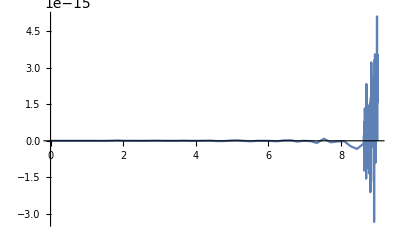

```mathematica
Plot[GC11[t],{t,0,9},PlotRange->All]
```

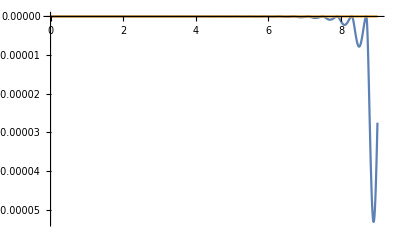

```mathematica
Plot[{GC1[t],GC11[t]},{t,0,9},PlotRange->All]
```

```mathematica
GC2[t_]= A31[t]P11[t]+A32[t]P12[t]-A11[t]P31[t]-A12[t]P32[t];
```

```mathematica
GC3[t_]= A21[t]P11[t]+A22[t]P12[t]-A11[t]P21[t]-A12[t]P22[t];
```

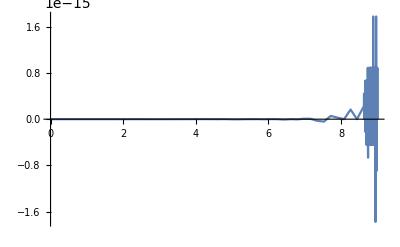

```mathematica
Plot[GC2[t],{t,0,9},PlotRange->All]
```

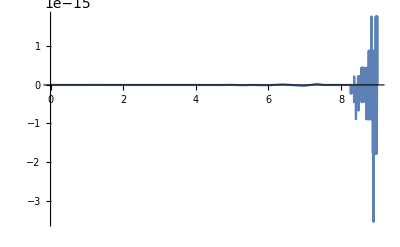

```mathematica
Plot[GC3[t],{t,0,9},PlotRange->All]
```